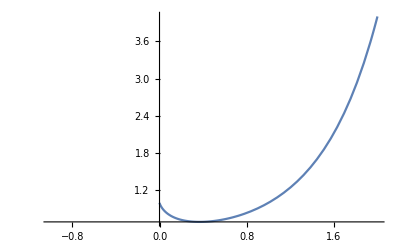

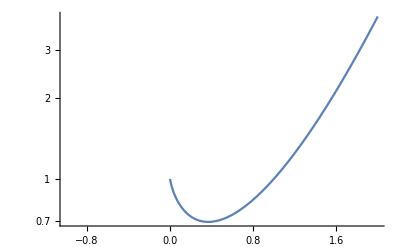

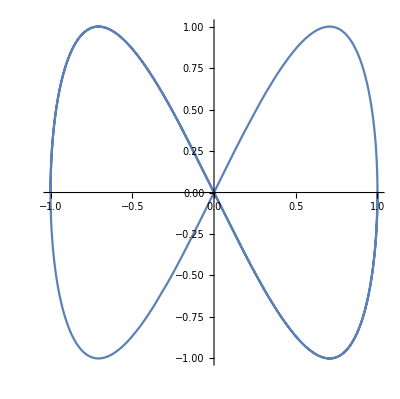

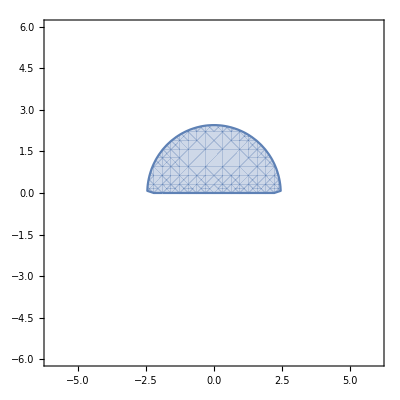

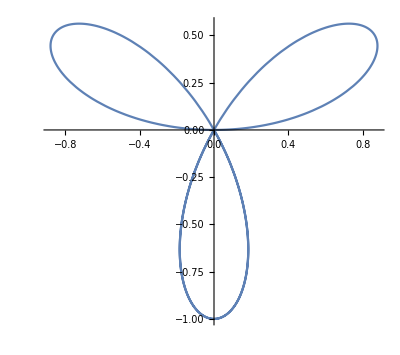

```mathematica
(* 绘制参数图 相当于极坐标 需要给出两个方程 其中一个作为横坐标 另外一个作为纵坐标 *)
```

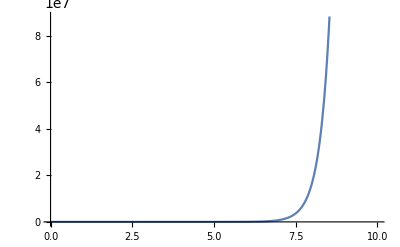

```mathematica
Plot[x^x, {x,0,10}]
```

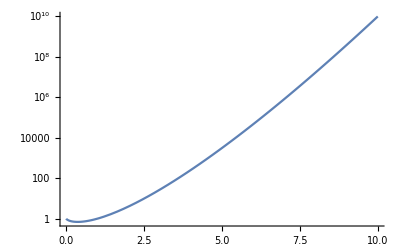

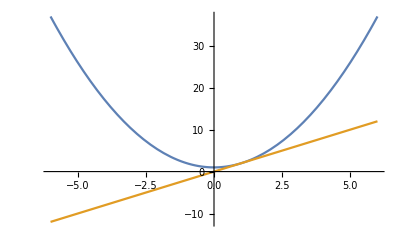

```mathematica
LogPlot[x^x,{x,0,10}]
```

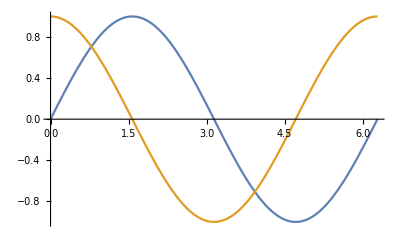

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π}]
```

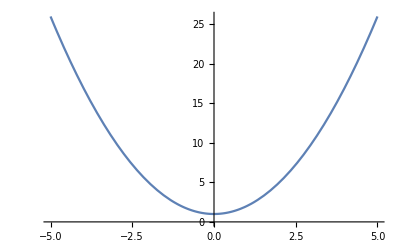

```mathematica
(* 绘制用户定义的函数 *)
Plot[x^2+1,{x,-5,5}]
```

```mathematica
f[x_]:=x^2+1;
```

```mathematica
Plot[f[x],{x,-5,5}]
```

-Graphics-

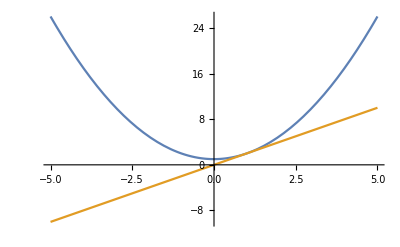

```mathematica
Plot[{f[x],f'[x]},{x,-5,5}]
```

```mathematica
(* 定义分段函数 面板->数学助手->高级->分段函数 点击Ctrl+Enter增加一行 *)
```

```mathematica
h[x_]:=Piecewise[{{2x, x<0}, {x^2, 0<=x<2}, {x, x>2}}]
```

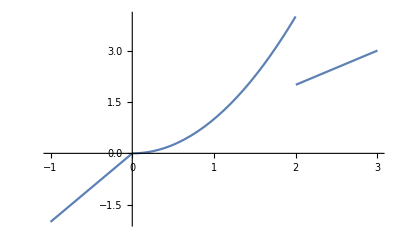

```mathematica
Plot[h[x],{x,-1,3}]
```



```mathematica
(* 底层绘图技术 *)
Plot[Sin[x],{x,0,2π}]
```

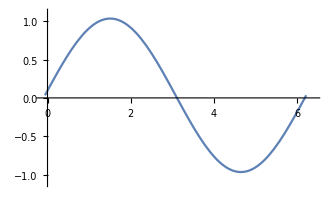

-Graphics-

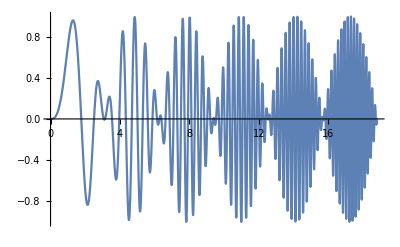

```mathematica
Plot[Sin[x]Sin[x^2],{x,0,6π}]
```

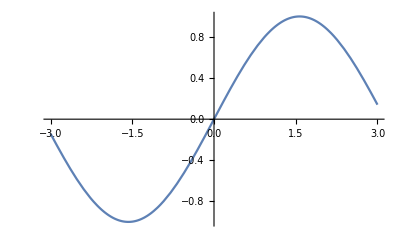

```mathematica
(* 可视化多元函数和表达式 *)
Plot[Sin[x],{x,-3,3}]
```

```mathematica
Plot3D[Sin[x * y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{4+(3+Cos[v])Sin[u],4+(3+Cos[v])Cos[u],4+Sin[v]},{u,0,2π},{v,0,2π},Mesh->All]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x]Cos[y],{x,-3,3},{y,-3,3},Mesh->All]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x]Cos[y],{x,-3,3},{y,-3,3},Mesh->None]
```

-Graphics3D-

```mathematica
(* 同时绘制多个三维曲面 *)
Plot3D[{Sin[x y],Cos[x y]},{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
(* 其他可视化类型 *)
RevolutionPlot3D[Sin[t]Sin[t^2],{t,0,π}]
```

-Graphics3D-

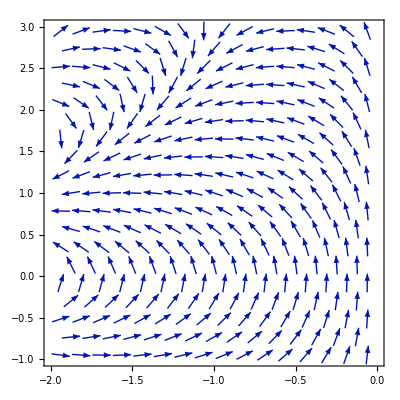

```mathematica
(* 绘制向量场 *)
VectorPlot[{Sin[x y],Cos[x y]},{x,-2,0},{y,-1,3}]
```

```mathematica
(* 绘制三维向量场 *)
VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

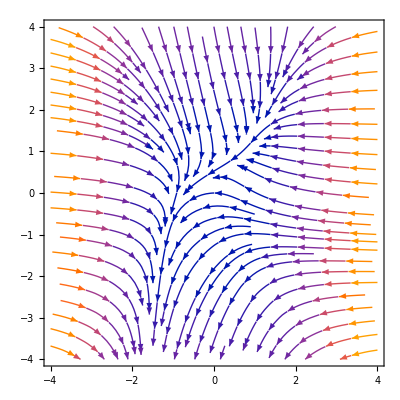

```mathematica
StreamPlot[{-1-x^3+y,x-y^2},{x,-4,4},{y,-4,4}]
```

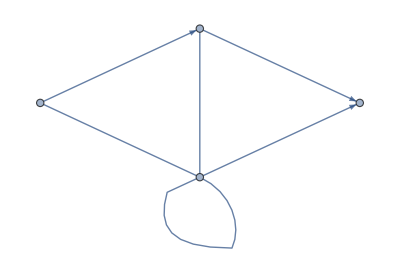

```mathematica
Graph[{
	1<->2,2<->3,3->1,2->4,1->4,2<->2
}](* <-> -> Esc ue Esc ;  -> -> Esc de Esc *)
```

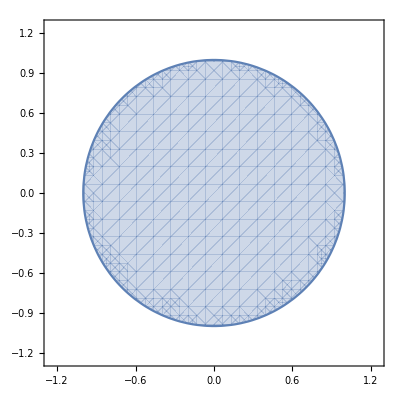

```mathematica
(*  不等式区域的绘制 *)
RegionPlot[x^2+y^2<=1,{x,-1.25,1.25},{y,-1.25,1.25},Axes->True]
```

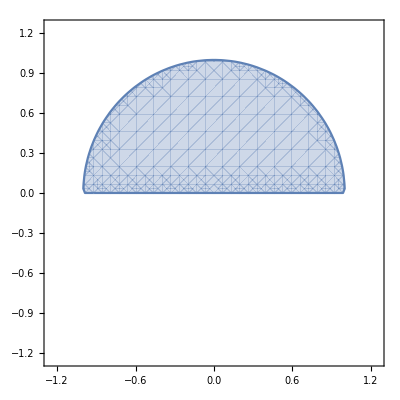

```mathematica
RegionPlot[x^2+y^2<=1 && y>=0,{x,-1.25,1.25},{y,-1.25,1.25},Axes->True]
```

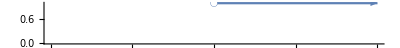

```mathematica
NumberLinePlot[x>1,{x,0,2}]
```

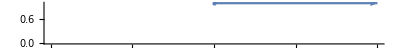

```mathematica
NumberLinePlot[x>=5,{x,0,10}]
```

```mathematica
NumberLinePlot[Interval[{5,Infinity}]]
```

-Graphics-

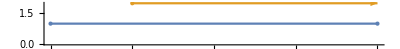

```mathematica
NumberLinePlot[{Interval[{1,5}],Interval[{2,Infinity}]}]
```

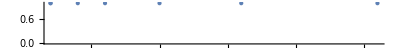

```mathematica
NumberLinePlot[{1,1,2,3,5,8,13}]
```

```mathematica
Manipulate[
	RegionPlot[x^2+y^3<n,{x,-2,2},{y,-2,2}],
	{n,-1,1}
]
```